```mathematica
$MinPrecision=50;
```

```mathematica
G=1/((3*10^5)^2);
ϵ="e";μ="μ";τ="τ";

Subscript[f, π]=130;
Subscript[V, ud]=0.974;
Subscript[M, ϵ]=0.511; Subscript[M, μ]=105; Subscript[M, τ]=1777;Subscript[M, π0]=135;Subscript[M, π]=139.5;
γ[m_]:=(G^2 m^5)/(192 π^3);
Γννν[m_]:=γ[m](Subscript[θ, ϵ]^2+Subscript[θ, μ]^2+Subscript[θ, τ]^2);
Γllν[m_,α_,α_]:=Return[0];
Γllν[m_,α_,β_]:=If[Subscript[M, α]+Subscript[M, β]<m,1,0]γ[m] Subscript[θ, α]^2(1-8 x^2+8 x^6-x^8-12 x^4 Log[x^2])/.x->Max[Subscript[M, α],Subscript[M, β]]/m;

w=0.2397;
Subscript[C, 1]=1/4(1-4w+8 w^2); Subscript[C, 3]=1/4(1+4w+8 w^2);
Subscript[C, 2]=1/2 w(2w-1); Subscript[C, 4]=1/2 w(2w+1);
L[x_]:=Log[(1-3 x^2-(1-x^2)√(1-4 x^2))/(x^2(1+√(1-4 x^2)))];
Γνll[m_,α_,β_]:=If[Subscript[M, α]+Subscript[M, β]<m,1,0]γ[m] Subscript[θ, α]^2(
If[α≠β,Subscript[C, 1],Subscript[C, 3]]((1-14 x^2-2 x^4-12 x^6)√(1-4 x^2)+12 x^4(x^4-1)L[x])+
4If[α≠β,Subscript[C, 2],Subscript[C, 4]](x^2(2+10 x^2-12 x^4)√(1-4 x^2)+6 x^4(1-2 x^2+2 x^4)L[x])
)/.x->SetAccuracy[Subscript[M, β]/m,100];
Γπν[m_,α_]:=If[Subscript[M, π0]<m,1,0] Subscript[θ, α]^2/(32π)G^2 Subscript[f, π]^2 m^3(1-Subscript[M, π0]^2/m^2)^2;
Γπl[m_,α_]:=If[Subscript[M, π]+Subscript[M, α]<m,1,0] Subscript[θ, α]^2/(16π)G^2 Subscript[V, ud]^2 Subscript[f, π]^2 m^3((1-Subscript[M, α]^2/m^2)^2-Subscript[M, π]^2/m^2(1+Subscript[M, α]^2/m^2))√((1-(Subscript[M, π]-Subscript[M, α])^2/m^2)(1-(Subscript[M, π]+Subscript[M, α])^2/m^2));
```

```mathematica
Γ[m_]:=2Re[
Γννν[m]+(
Total[Γllν[m,#⟦1⟧,#⟦2⟧]+Γνll[m,#⟦1⟧,#⟦2⟧]&/@Tuples[{ϵ,μ,τ},2]]
)+(
Total[Γπν[m,#]+Γπl[m,#]&/@{ϵ,μ,τ}]
)
];
```

```mathematica
MEVtoSEC[mev_]:=(6.582 10^-22)/mev;
```

```mathematica
θs[z_:1]:={Subscript[θ, ϵ]->z/(√m)√(1.3 10^-8),Subscript[θ, μ]->z/(√m)√(3.8 10^-7),Subscript[θ, τ]->z/(√m)√(3.2 10^-7)}
```

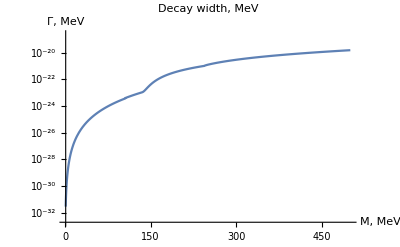
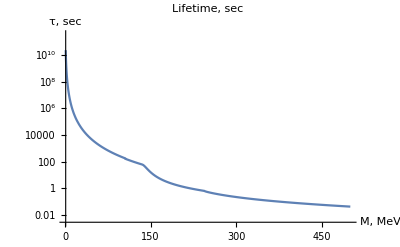

```mathematica
Row[{LogPlot[Γ[m]/.θs[],{m,1,500},PlotRange->All,PlotLabel->"Decay width, MeV",AxesLabel->{"M, MeV","Γ, MeV"},PlotPoints->150,ImageSize->400],
LogPlot[MEVtoSEC[Γ[m]/.θs[]],{m,1,500},PlotRange->All,PlotLabel->"Lifetime, sec",AxesLabel->{"M, MeV","τ, sec"},PlotPoints->150,ImageSize->400]
}]
```

```mathematica
LogarithmicScaling[x_,min_,max_]:=Log[x/min]/Log[max/min];
Show[
ContourPlot[
(MEVtoSEC[Γ[m]]/.θs[10^(y+4)]),
{m,00,500},{y,-6,-2},
Contours->{0.01,0.1,0.3,1,10,100,1000},
ContourLabels->All,
ColorFunctionScaling->False,ContourShading->None
],GridLines->{{{33.9,Dashed},135,490},{}},
PlotLabel->"Sterile neutrino lifetimes",
FrameLabel->{"Mass, MeV","log_10(θ)"}
]
```

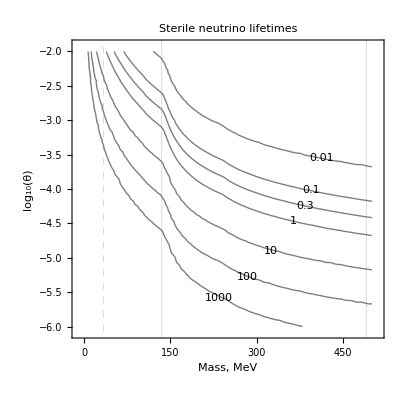

```mathematica
Γγ[m_,T_]:=NIntegrate[T^4/m(e^2 √(e^2-(m/T)^2))/(E^e+1),{e,m/T,∞}];
Plot3D[Γγ[m,T],{T,300,1},{m,135,490}]
```

-Graphics3D-

NIntegrate::inumr: The integrand 150\ p^2/(1 + ⅇ^√90000 + Power[« 2 »]/T)\ √90000 + p^2\ π^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand p^2/2\ (1 + ⅇ^√90000 + Power[« 2 »]/T)\ π^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

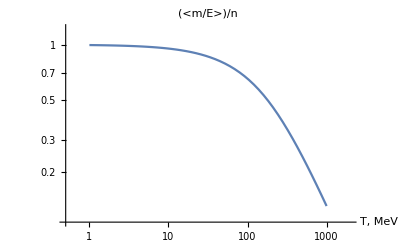

```mathematica
RelativisticCorrection[m_]:=(
LogLogPlot[
NIntegrate[(m p^2)/(2 π^2)1/(√(p^2+m^2))1/(E^((√(p^2+m^2))/T)+1),{p,0,∞}]/NIntegrate[p^2/(2 π^2)1/(E^((√(p^2+m^2))/T)+1),{p,0,∞}],
{T,1000,1},PlotLabel->"(<m/E>)/n",AxesLabel->{"T, MeV"}]
);
RelativisticCorrection[300]
```